```mathematica
SetDirectory["~/Code/mesons/data"];
Needs["PlotLegends`"];
```

```mathematica
bPoints=Import["bottom_points.csv"];
cPoints=Import["charm_points.csv"];

bLine=Fit[bPoints,{1,x},x]
```

9.01124+0.230043 x

```mathematica
cLine=Fit[cPoints,{1,x},x]
```

2.42771+0.296892 x

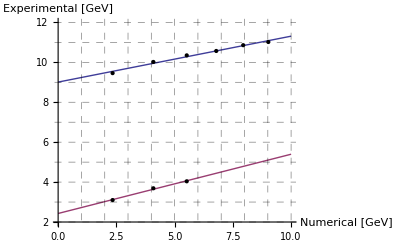

```mathematica
(*Show[*)
Plot[
{bLine,cLine},{x,0,10},
PlotRange->{{0,10.01},{2,12}},
GridLines->{Range[12],Range[12]},
GridLinesStyle->Directive[Black,Opacity[0.5],Dashed],
Epilog->{PointSize[Medium],Point[bPoints],Point[cPoints]},
AxesLabel->{"Numerical\n[GeV]","Experimental\n[GeV]"},
PlotLegend->{"Bottom","Charm"},
LegendPosition->{0.8,0},
LegendShadow->None,
LegendTextSpace->10,
LegendBorder->None
]
```

```mathematica
airyOne=Import["airy_one.csv"];
```

```mathematica
airyTwo=Import["airy_two.csv"];
```

```mathematica
airyThree=Import["airy_three.csv"];
```

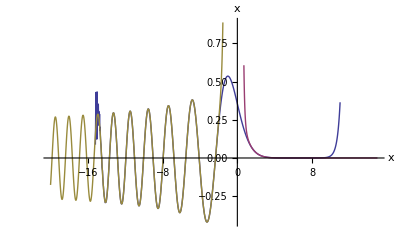

```mathematica
ListLinePlot[
{airyOne,airyTwo,airyThree},
AxesLabel->{Style[x,13],Style[AiryAi[x],13]},
PlotLegend->{Style["First",13],Style["Second",13],Style["Third",13]},
LegendPosition->{0.6,0.2},
LegendShadow->None,
LegendBorder->None,
LegendTextSpace->8
]
```